# Chapter 6 Smoothing Data, Filling Missing Data, and Nonparametric Fitting

Here we discuss dangerous techniques: smoothing data to eliminate noise and filling in missing data values. The reason for the danger is that any such method assumes that the data does not contain small-scale structure, although often nothing supports the assumption except the analyst’s hunch or hope.

This chapter also discusses fitting data when a model is either not available or not desired: this is called “nonparametric” fitting.

## 6.1 Introduction

### 6.1.1 Smoothing with Averaging Techniques

Often one is confronted with “noisy” data. For example, here is a “chirp” signal.

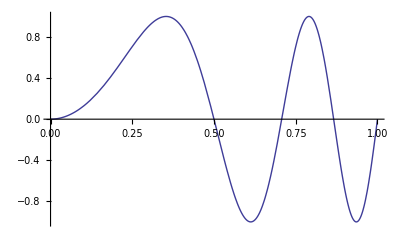

```mathematica
Plot[Sin[4 π t^2],{t,0,1}]
```

The signal is so named because it resembles the chirp of a bird.

Perhaps the signal has noise.

```mathematica
SeedRandom[1234];mydata=Table[N[Sin[4 π t^2]+Random[NormalDistribution[0,0.5]]],{t,0,1,1/4999}];
```

```mathematica
Needs["EDA`"]
```

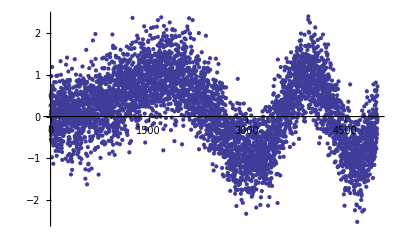

```mathematica
EDAListPlot[mydata]
```

Here the noise is a randomized Gaussian with mean of 0 and standard deviation of 0.5. In this example, we have 500 data points.

The routine that generated this data is supplied as part of the EDA`SmoothData` package.

```mathematica
? SmoothTestData
```

SmoothTestData[number, stddev] generates number data points which are
	of the form Sin[4Pi t^2] for t between 0 and 1, with a Gaussian noise
	of standard deviation stddev added. If the option ExtraSignal is set
	to True, a sine wave of period 0.05 and amplitude 0.5 is added to the
	chirp between t = 0.4 and t = 0.45.

One technique to smooth the data is to take overlapping subsets of the data and average the values of each. We will illustrate with a very simple data set.

```mathematica
mydata2={1,2,3,4,5,6,7,8,9,10};
```

The following line calculates the mean by adding up all the elements of the list and dividing by the length of the list.

```mathematica
mymean[y_]:=N[(Plus@@y)/Length[y]]
```

```mathematica
mymean[mydata2]
```

5.5

The built-in Mathematica function Partition divides its input into partitioned subsets.

```mathematica
Partition[mydata2,5,1]
```

{{1,2,3,4,5},{2,3,4,5,6},{3,4,5,6,7},{4,5,6,7,8},{5,6,7,8,9},{6,7,8,9,10}}

We can find the average of each subset.

```mathematica
mymean/@Partition[mydata2,5,1]
```

{3.,4.,5.,6.,7.,8.}

We apply this idea to the noisy chirp signal, with 43 points in each subset.

```mathematica
smoothed=mymean/@Partition[mydata,43,1];
```

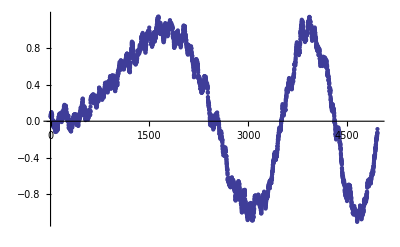

```mathematica
EDAListPlot[smoothed]
```

Note that this procedure ends up with less data than the input.

```mathematica
{Length[mydata],Length[smoothed]}
```

{5000,4958}

The EDA function SmoothData uses almost exactly the same method by default.

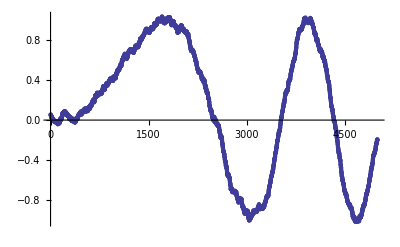

```mathematica
EDAListPlot[SmoothData[mydata]]
```

Here is the default number of points in the subsets.

points=2*Floor[Sqrt[[Length[mydata]]]]-1

For this data the number of points is equal to 43.

Near the left- and right-hand sides, SmoothData has constructed subsets of the data with fewer than points members; thus it returns the same number of data points as mydata. Of course, with fewer points the averaging at these sides will be somewhat “wilder”.

The number of points can be controlled with an option.

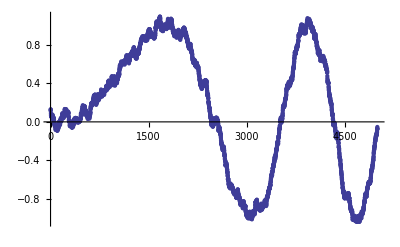

```mathematica
EDAListPlot[SmoothData[mydata,Points->75]]
```

This smooths the data more than the previous example but has lost some information, particularly at the right-hand side. Note also that the program systematically decreases the amplitude of the signal at larger values of t for this data.

Points should be an odd integer less than the number of data points.

A similar method of smoothing data is based on the realization that the value at the center of each subset is more likely to be close to the actual data point than values at the ends of the subset. Thus, you can weight the values in the subset. Typically, a parabolic weight 1 - (t - t0)^2 is used, normalized so the area under the curve is 1. Thus, this is what the weighting looks like.

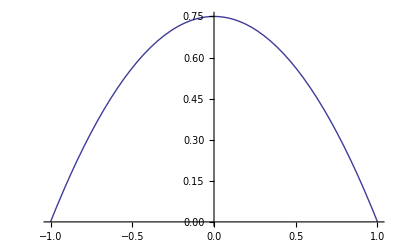

```mathematica
t0=0;Plot[0.75 (1-(t-t0)^2),{t,-1,1}]
```

SmoothData provides an option for this type of weighting.

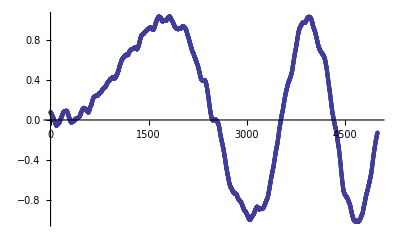

```mathematica
EDAListPlot[SmoothData[mydata,Method->WeightedAverage]]
```

The number of points in each partition can also be adjusted.

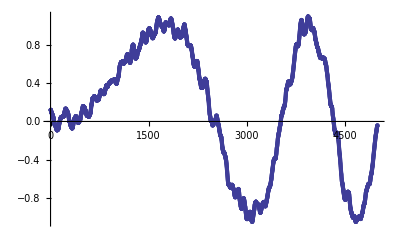

```mathematica
EDAListPlot[SmoothData[mydata,Method->WeightedAverage,Points->75]]
```

Although not an issue for this example data set, taking the average of the subset can lead to problems if the noise signal contains large variations. This is because one wild data point can seize control of an average, which will affect the result of each partition of the data in which it appears. A more robust operation than the average is the median. SmoothData can use the median.

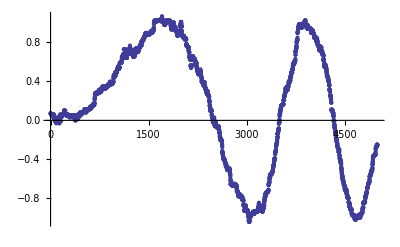

```mathematica
EDAListPlot[SmoothData[mydata,Method->SimpleMedian]]
```

For this data, this procedure yields the least smooth of the three methods.

We construct a dataset for which there is one wild data point out of the 500 total points.

```mathematica
data2=mydata;data2⟦200⟧=15;
```

The effect on the two averaging methods is large.

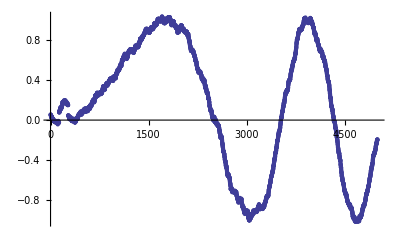

```mathematica
EDAListPlot[SmoothData[data2]]
```

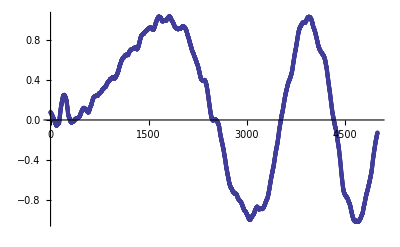

```mathematica
EDAListPlot[SmoothData[data2,Method->WeightedAverage]]
```

But the median is robust.

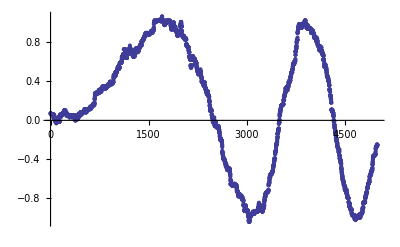

```mathematica
EDAListPlot[SmoothData[data2,Method->SimpleMedian]]
```

Finally, imagine the chirp signal also has a small sine wave added for a region.

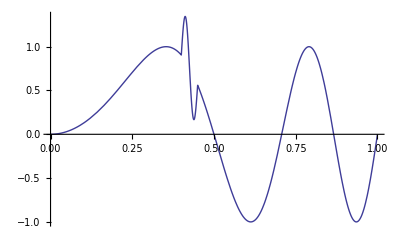

```mathematica
Plot[Sin[4 π t^2]+If[t>0.4&&t<0.45,0.5 Sin[(2 π t)/0.05],0],{t,0,1}]
```

We add random noise as before, this time with a standard deviation of 0.1. As a convenience, a routine to generate test data is included named SmoothTestData. We use it to generate a data set.

```mathematica
data3 = SmoothTestData[500, 0.1, ExtraSignal -> True];
```

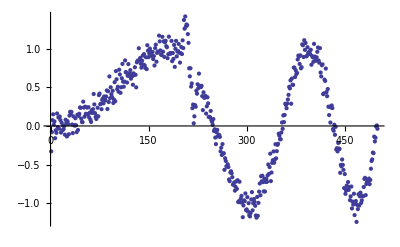

```mathematica
EDAListPlot[data3]
```

SmoothData misses the small structure almost entirely.

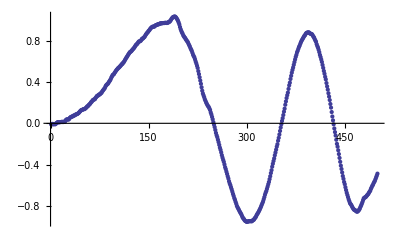

```mathematica
EDAListPlot[SmoothData[data3]]
```

We can reduce the number of points to preserve the structure.

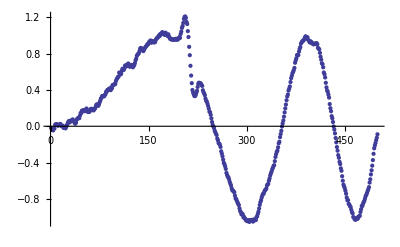

```mathematica
EDAListPlot[SmoothData[data3,Points->11]]
```

This illustrates the danger referred to at the beginning: blindly using SmoothData or any other smoothing algorithm can cause real structure in the data to be lost. As Press, et al., say, think about “letting it all hang out. (Have you considered showing the data as they actually are?)” [Numerical Recipes in C, p. 514].

### 6.1.2 Fourier Filters

SmoothData can use another method, based on the Fourier transform.

If, as in our examples, the signal is a function of time, then the Fourier transform of the signal is a function of the frequency. We can weight the transform to suppress the high-frequency components and then take the inverse Fourier transform to produce a filtered signal.

We use the same data as in the previous subsection and smooth it using a Fourier filter.

```mathematica
SeedRandom[1234];mydata=Table[N[Sin[4 π t^2]+Random[NormalDistribution[0,0.5]]],{t,0,1,1/4999}];
```

```mathematica
Needs["EDA`"]
```

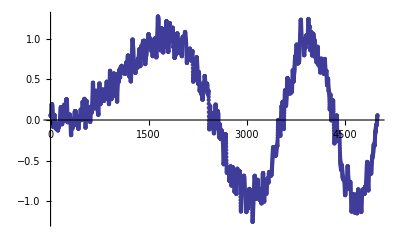

```mathematica
EDAListPlot[SmoothData[mydata,Method->WeightedFourier]]
```

For this method, the weighting is a Gaussian centered at zero frequency. Points is the number of frequency points corresponding to the standard deviation squared of the Gaussian. Thus, as opposed to the averaging methods, decreasing the number of points increases the smoothing.

For example, the previous plot is for the default of 43 points. Here is the result for 11 points.

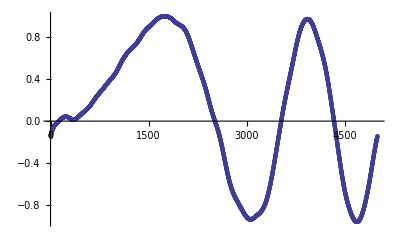

```mathematica
EDAListPlot[SmoothData[mydata,Method->WeightedFourier,Points->11]]
```

The method is not very robust. Using the data from the previous subsection with one wild point shows that a single data point can have a large effect.

```mathematica
data2=mydata;data2⟦200⟧=15;
```

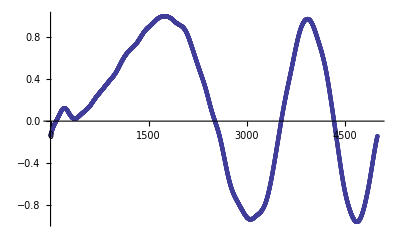

```mathematica
EDAListPlot[SmoothData[data2,Method->WeightedFourier,Points->11]]
```

We can reduce the number of frequency points to reduce this effect.

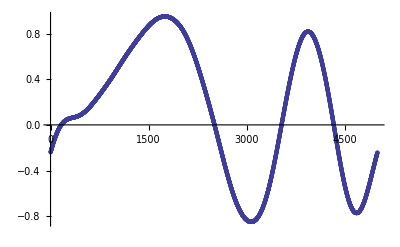

```mathematica
EDAListPlot[SmoothData[data2,Method->WeightedFourier,Points->5]]
```

For the signal with a small sine wave added to a region, the default number of points keeps the small added term in the smoothed spectrum.

```mathematica
data3 = SmoothTestData[500, 0.1, ExtraSignal -> True];
```

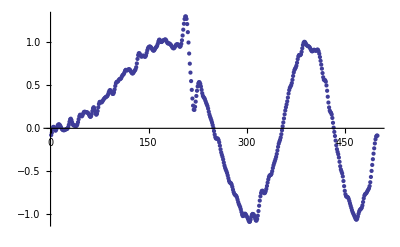

```mathematica
EDAListPlot[SmoothData[data3,Method->WeightedFourier]]
```

We can filter out the high-frequency signal.

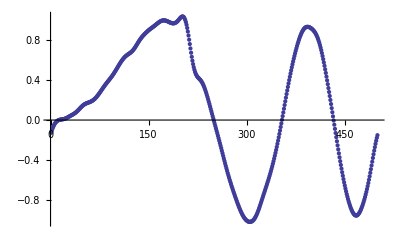

```mathematica
EDAListPlot[SmoothData[data3,Method->WeightedFourier,Points->11]]
```

### 6.1.3 Loess Fitting

As hikers know, loess is a surface of loam such as is deposited by the wind. Loess fitting is similar to the method using WeightedAverage that can optionally be used by SmoothData, as described in Section 6.1.1. However, here we take each weighted subset of the data and fit it to either a straight line or a second- or third-order polynomial.

We loess fit the same noisy chirp signal, mydata, that we have used throughout this chapter, to a second-order polynomial.

```mathematica
SeedRandom[1234];mydata=Table[N[Sin[4 π t^2]+Random[NormalDistribution[0,0.5]]],{t,0,1,1/4999}];
```

```mathematica
Needs["EDA`"]
```

```mathematica
EDAListPlot[mydata]
```

-Graphics-

```mathematica
result=LoessFit[mydata,2];
```

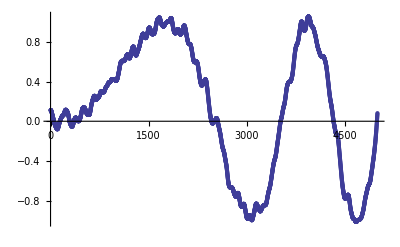

```mathematica
EDAListPlot[result]
```

The second parameter in the call to LoessFit must be either 1, 2, or 3, giving a first-order, second-order, or third-order polynomial fit, respectively.

In addition, just as for SmoothData, the number of points in each subset may be set using the Points option, which should be set to an odd integer.

An extensive discussion of the LoessFit method appears in William S. Cleveland, Visualizing Data (AT&T Bell Laboratories, 1993). Cleveland uses a parameter alpha to choose the number of points.

points=alpha*Length[data]

LoessFit can accept an EDAAlpha option as a way of choosing the points.

```mathematica
?EDAAlpha
```

EDAAlpha is an option for LoessFit that selects the number of points
	used in each subset of the data. Automatic (the default) uses
	2*Floor[Sqrt[Length[data]]] + 1 points. Otherwise, the points are
	equal to the value of EDAAlpha times the number of data points in the
	data, rounded to the nearest odd integer. EDAAlpha should be a positive
	number. Note that the Points option provides another way
	to choose the points. The EDAAlpha option is used to make LoessFit
	more notationally consistent with William S. Cleveland, "Visualizing
	Data" (AT&T Bell Laboratories, 1993).

SmoothData[ ... , Method -> WeightedAverage] uses a parabolic weighting. LoessFit uses a tricubic weighting.

w=(1-Abs[delta]^3)^3

Here delta is between -1 and 1. This is what that weighting looks like.

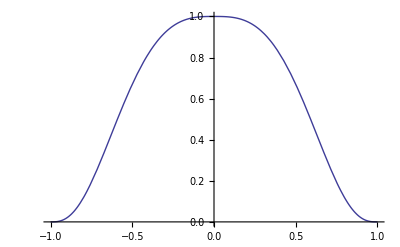

```mathematica
Plot[(1-Abs[delta]^3)^3,{delta,-1,1}]
```

While loess fitting can be viewed as a data-smoothing technique, it can also be thought of as a fit to a data set when we cannot expect to find a parametric family, such as a straight line, to model the data. Thus it is a nonparametric fitter.

As opposed to SmoothData, LoessFit can process data with the value of Points greater than the number of data points. In this case, the weights are divided by (Points / number of data points).

Because each partition of the data set is individually fit to a line or a second- or third-order polynomial, as a data smoother LoessFit is the slowest of the techniques discussed so far in this chapter.

For example, here are some timings on a particular computer.

```mathematica
First[Timing[SmoothData[mydata];]]
```

0.281

```mathematica
First[Timing[SmoothData[mydata,Method->WeightedAverage];]]
```

2.891

```mathematica
First[Timing[SmoothData[mydata,Method->SimpleMedian];]]
```

0.172

```mathematica
First[Timing[SmoothData[mydata,Method->WeightedFourier];]]
```

0.094

```mathematica
First[Timing[LoessFit[mydata,1];]]
```

7.109

This timing is hardly surprising since LoessFit in this case performs 5000 straight-line fits using the Mathematica function Fit.

However, as a nonparametric fitter LoessFit can sometimes be very useful. For example, in Chapter 4 we were trying to decide whether some data on the ganglia of cat fetuses were best modeled by a straight line or a parabola. We repeat two fits from that chapter.

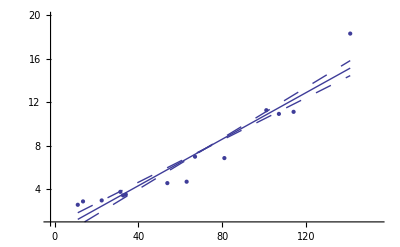

{a[0]→{0.03,0.72},a[1]→{0.107,0.01},PseudoErrorY→1.45358,SumOfSquares→25.3546,DegreesOfFreedom→12,Residuals→{{11.1,{1.3,1.5}},{13.6,{1.4,1.5}},{22.5,{0.5,1.5}},{31.4,{0.4,1.5}},{32.7,{-0.1,1.5}},{34.,{-0.2,1.5}},{53.8,{-1.2,1.5}},{63.,{-2.1,1.5}},{67.,{-0.2,1.5}},{81.,{-1.8,1.5}},{101.,{0.4,1.5}},{107.,{-0.6,1.5}},{114.,{-1.1,1.5}},{141.,{3.2,1.5}}}}

```mathematica
result1=LinearFit[GanglionData,{0,1},a,ReturnResiduals->True]
```

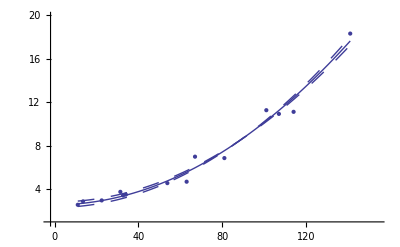

{a[0]→{2.56,0.25},a[2]→{0.000757,0.000032},PseudoErrorY→0.692244,SumOfSquares→5.75043,DegreesOfFreedom→12,Residuals→{{11.1,{-0.09,0.69}},{13.6,{0.17,0.69}},{22.5,{0.02,0.69}},{31.4,{0.44,0.69}},{32.7,{0.05,0.69}},{34.,{0.06,0.69}},{53.8,{-0.2,0.69}},{63.,{-0.88,0.69}},{67.,{1.02,0.69}},{81.,{-0.68,0.69}},{101.,{0.97,0.69}},{107.,{-0.32,0.69}},{114.,{-1.3,0.69}},{141.,{0.68,0.69}}}}

```mathematica
result2=LinearFit[GanglionData,{0,2},a,ReturnResiduals->True]
```

We display the residuals and a LoessFit to them for the first fit.

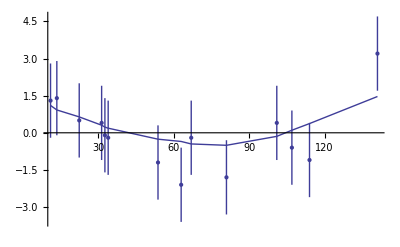

```mathematica
Show[{EDAListPlot[Residuals/.result1,DisplayFunction->Identity, PlotRange -> All],EDAListPlot[LoessFit[Residuals/.result1,1,Points->13],Joined->True,DisplayFunction->Identity]},DisplayFunction->$DisplayFunction]
```

The joined points show the smoothing effect of LoessFit.

We repeat for the second fit.

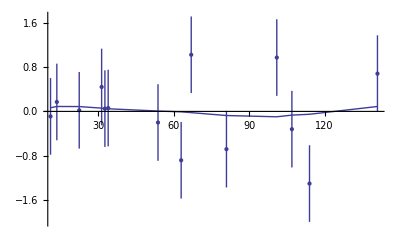

```mathematica
Show[{EDAListPlot[Residuals/.result2,DisplayFunction->Identity, PlotRange -> All],EDAListPlot[LoessFit[Residuals/.result2,1,Points->13],Joined->True,DisplayFunction->Identity]},DisplayFunction->$DisplayFunction]
```

As can be seen, the residuals for this second fit are much closer to zero, and are consistent with having zero slope. This is further indication of the fact, discussed in Chapter 4, that this data appears to be better fit by a parabola than a straight line.

### 6.1.4 Using Mathematica Built-in Functions

The richness of Mathematica often provides just the tools needed to do a particular analysis without needing to load any packages from EDA. Here we provide a small example using some mass spectrometer data.

```mathematica
Needs["EDA`"]
```

```mathematica
LoadData[MassSpec2]
```

LoadData::name: Loading: MassSpec2Data

```mathematica
?MassSpec2Data
```

MassSpec2Data is ionization data for neon from a mass
	spectrometer. The data was collected by an apparatus in the
	undergraduate laboratories of the Dept. of Physics, Univ.
	of Toronto, during the Winter of 1993, by Mr. Youri Zabbal,
	when he was an undergraduate student. The format is 
	{voltage, current}, where the voltage is in volts and the
	current is in mA.

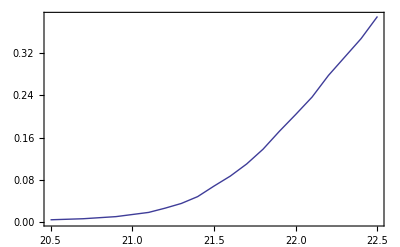

```mathematica
ListPlot[MassSpec2Data,Axes->False,Frame->True,Joined->True]
```

If the instrument resolution were perfect, we would expect the plot to be discontinuous. For example, if the ionization voltage were 21.5 volts, the plot would look like this.

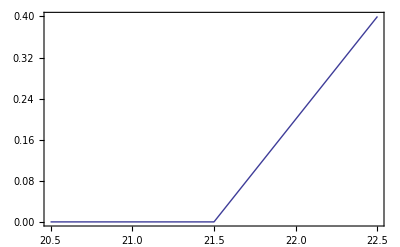

```mathematica
Plot[If[v<21.5,0,0.4 (v-21.5)],{v,20.5,22.5},Axes->False,Frame->True]
```

We form and examine an interpolation of the data.

```mathematica
int=Interpolation[MassSpec2Data]
```

InterpolatingFunction[{{20.5,22.5}},<>]

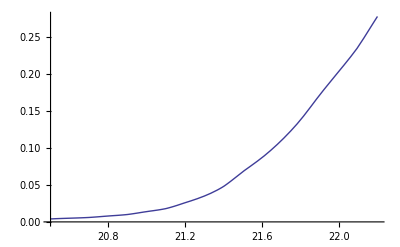

```mathematica
Plot[int[voltage],{voltage,20.5,22.2}]
```

We take the derivative of the interpolation and then plot it.

```mathematica
dint=D[int[voltage], voltage]
```

InterpolatingFunction[{{20.5,22.5}},<>][voltage]

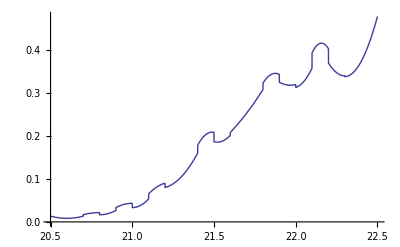

```mathematica
Plot[dint,{voltage,20.5,22.5}]
```

Note that the plot is not smooth. The reason is that Interpolation is constrained to go exactly through every data point. When there is a small amount of noise in the data, this constraint leads to a jagged first derivative.

The second derivative is even worse.

```mathematica
ddint=D[dint, voltage]
```

InterpolatingFunction[{{20.5,22.5}},<>][voltage]

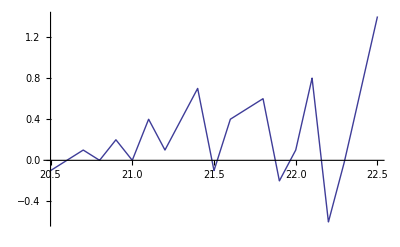

```mathematica
Plot[ddint,{voltage,20.5,22.5}]
```

We will use the SmoothData function discussed in Section 6.1.1.1 to construct a “smoothed” table of values for the first derivative. We generate 50 points and have SmoothData smooth them in groups of 15.

```mathematica
dv=(22.5-20.5)/(50-1)
```

0.0408163

```mathematica
dsmooth=SmoothData[Table[{voltage,dint},{voltage,20.5,22.5,dv}],Points->15];
```

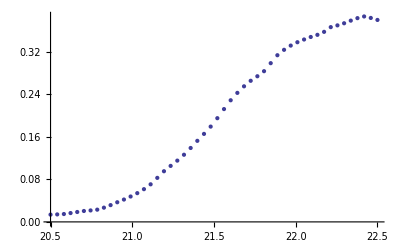

```mathematica
EDAListPlot[dsmooth]
```

This plot looks much better.

```mathematica
N[Last[dsmooth],30]
```

{22.5,0.380413}

We construct an interpolation of this data.

```mathematica
sdint=Interpolation[dsmooth]
```

InterpolatingFunction[{{20.5,22.5}},<>]

We take the derivative.

```mathematica
ddint=D[sdint[voltage], voltage]
```

InterpolatingFunction[{{20.5,22.5}},<>][voltage]

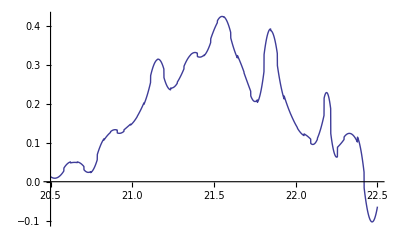

```mathematica
Plot[ddint,{voltage,20.5,22.5}]
```

We smooth ddint.

```mathematica
ddsmooth=SmoothData[Table[{voltage,ddint},{voltage,20.5,22.5,dv}],Points->15];
```

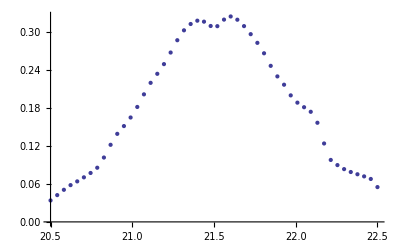

```mathematica
EDAListPlot[ddsmooth]
```

So, we conclude that the maximum in the second derivative is about 21.5 ± 0.2 volts. This is the technique used by the EDA function FindPeaks described in Chapter 8.

### 6.1.5 Filling Missing Data

Most of EDA deals with the most common form of data encountered in science and engineering: {x, y} pairs, possibly with errors in one or both coordinates. For such “bivariate” data, finding a value for a missing data point is usually easy. If we have a model for the data, we can fit the data to the model and evaluate the fit result at the missing point; if we lack a model then the Mathematica built-in function Interpolation returns an InterpolatingFunction which can similarly be evaluated for the missing point.

If the data is a matrix of values, the EDA function FillData introduced here fills in missing values. Such a data structure is called “multivariate” since each data point in the matrix actually represents an {x, y, value} triple. We illustrate this with some data on ozone levels in the atmosphere.

```mathematica
Needs["EDA`"]
```

```mathematica
LoadData[Ozone]
```

LoadData::name: Loading: OzoneData

```mathematica
?OzoneData
```

OzoneData is data on ozone levels in the atmosphere on December 25,
	1988. The data was taken by the Total Ozone Measurement Spectrometer
	(TOMS) aboard the Nimbus 7 satellite. The 60 rows of data correspond
	to latitudes 50 degrees south to 10 degrees north in one degree bins.
	The 60 columns correspond to longitudes of 180 degrees west to 105 degrees
	west in 1.25 degree bins. The units of the data are Dobson units.

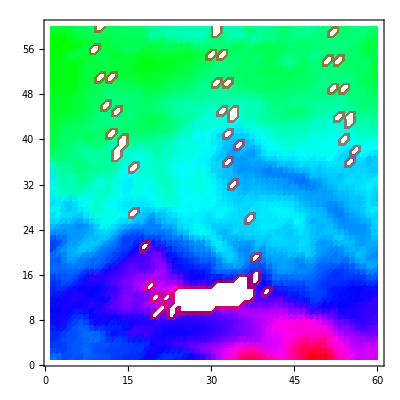

```mathematica
ListDensityPlot[OzoneData, ColorFunction -> Hue]
```

Nimbus 7 is in a south-north sun synchronous polar orbit such that it is always close to local noon/midnight beneath the satellite. The black areas in the plot are missing data; they are represented by values of 0. The small missing areas are because the width of data-taking does not completely overlap with the width of the next pass of the satellite; the larger missing area is due to a temporary failure in the down-link or perhaps a brief shutdown of the spectrometer for maintenance.

We will also be using the small made-up data sets myData1 and myData2. The latter is a 5 × 6 matrix with some structure, while the former has some missing values inserted.

```mathematica
myData1=Table[0,{5},{6}];
For[row=1,row≤5,row++,
		For[col=1,col≤6,col++,  myData1⟦row,col⟧=5+(row-2)^2+(col-3)^2;
		];
];
myData2=myData1;
myData1⟦3,2⟧=myData1⟦3,3⟧=myData1⟦2,6⟧=0;
myData1⟦3,6⟧=myData1⟦4,5⟧=myData1⟦4,6⟧=0;
myData1⟦5,5⟧=myData1⟦5,6⟧=myData1⟦2,3⟧=0;
```

```mathematica
MatrixForm[myData1]
```

(10 | 7 | 6 | 7 | 10 | 15
9 | 6 | 0 | 6 | 9 | 0
10 | 0 | 0 | 7 | 10 | 0
13 | 10 | 9 | 10 | 0 | 0
18 | 15 | 14 | 15 | 0 | 0)

Again, the missing values are represented by zeros, which are the black areas in the density plot.

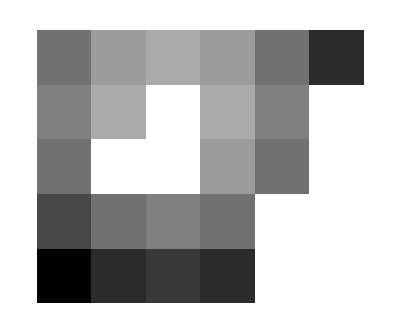

```mathematica
ArrayPlot[myData1]
```

The data set myData2 has no missing values, and a somewhat symmetric structure.

```mathematica
MatrixForm[myData2]
```

(10 | 7 | 6 | 7 | 10 | 15
9 | 6 | 5 | 6 | 9 | 14
10 | 7 | 6 | 7 | 10 | 15
13 | 10 | 9 | 10 | 13 | 18
18 | 15 | 14 | 15 | 18 | 23)

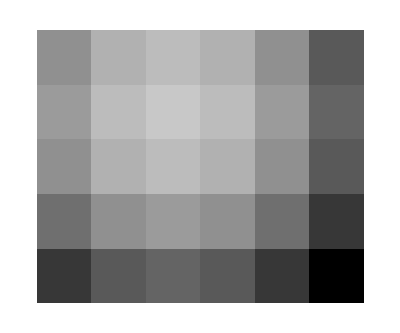

```mathematica
ArrayPlot[myData2]
```

FillData can fill in missing values.

```mathematica
fd=FillData[myData1];
```

```mathematica
MatrixForm[fd]
```

(10. | 7. | 6. | 7. | 10. | 15.
9. | 6. | 7. | 6. | 9. | 10.
10. | 9. | 6. | 7. | 10. | 9.
13. | 10. | 9. | 10. | 7. | 10.
18. | 15. | 14. | 15. | 10. | 0.)

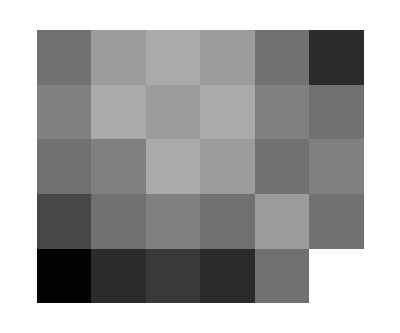

```mathematica
ArrayPlot[fd]
```

The default method for FillData, EDANearestNeighbor, is to fill the missing point with the value of a nearest adjacent neighbor. Since the point in the lower right had no non-missing neighbors, it was not filled. We can direct FillData to do two passes on the data by setting the MaximumIterations option to 2.

```mathematica
MatrixForm[FillData[myData1,MaximumIterations->2]]
```

(10. | 7. | 6. | 7. | 10. | 15.
9. | 6. | 7. | 6. | 9. | 10.
10. | 9. | 6. | 7. | 10. | 9.
13. | 10. | 9. | 10. | 7. | 10.
18. | 15. | 14. | 15. | 10. | 7.)

Now there are no missing values.

We can similarly use FillData on OzoneData.

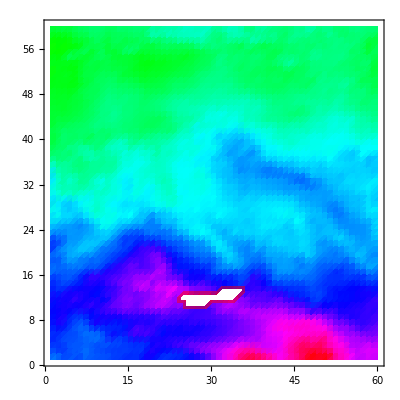

```mathematica
ListDensityPlot[FillData[OzoneData], ColorFunction -> Hue]
```

The small missing areas are filled and the large missing area is now smaller. A second iteration fills the large area entirely.

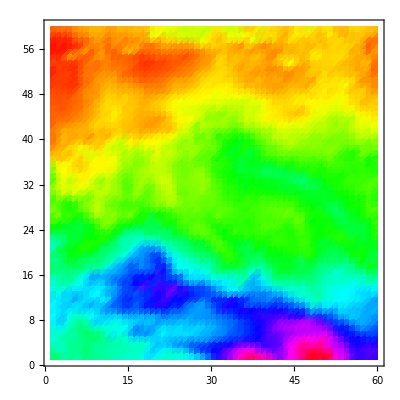

```mathematica
ListDensityPlot[FillData[OzoneData,MaximumIterations->2], ColorFunction -> Hue]
```

EDANearestNeighbor, the default Method used by FillData, is the fastest and simplest available. However, other methods are available.

The second simplest method for FillData is SmoothFill, in which each missing value is filled in with the average value of all the non-missing adjacent neighbors.

```mathematica
MatrixForm[FillData[myData1,Method->SmoothFill]]
```

(10. | 7. | 6. | 7. | 10. | 15.
9. | 6. | 6.5 | 6. | 9. | 11.
10. | 9.5 | 8. | 7. | 10. | 9.5
13. | 10. | 9. | 10. | 10.5 | 10.
18. | 15. | 14. | 15. | 12.5 | 0.)

This method does a nice job on the ozone data, but it works a little more slowly than EDANearestNeighbor.

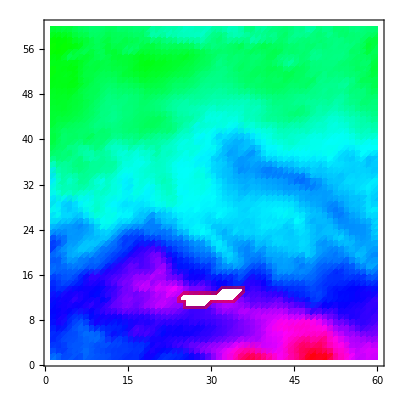

```mathematica
ListDensityPlot[FillData[OzoneData,Method->SmoothFill], ColorFunction -> Hue]
```

A related method reasons that if averaging is a good idea for filling in missing values, it is a better idea to average all the values in the data set.

```mathematica
MatrixForm[N[FillData[myData1,Method->SmoothFillAll],3]]
```

(8. | 7.6 | 6.4 | 7.6 | 9.4 | 11.3333
8.4 | 8. | 6.5 | 7.85714 | 9.14286 | 11.
9.6 | 9.5 | 8. | 8.5 | 8.4 | 9.5
13.2 | 12.7143 | 11.4286 | 10.8333 | 10.5 | 10.
14. | 13.1667 | 12.1667 | 12. | 12.5 | 0.)

Although this method can sometimes be useful, it is always dangerous to actually alter any real data points. Nonetheless, this method does smooth out noise in the data. In fact, one could smooth the data down to a uniform gray by repeated iterations except that FillData never attempts to work on data that has no missing values.

The final two related methods available to FillData are RowInterpolation and ColumnInterpolation. Each uses Mathematica’s Interpolation function to interpolate missing data; RowInterpolation interpolates the rows, ColumnInterpolation the columns. Note that the methods do not extrapolate to edges where there is missing data.

For myData1, nearly identical to myData2 but with added some missing values,the outputs of both RowInterpolation and ColumnInterpolation are identical and except for the missing data at the edges also duplicate the full data set.

```mathematica
MatrixForm[myData2]
```

(10 | 7 | 6 | 7 | 10 | 15
9 | 6 | 5 | 6 | 9 | 14
10 | 7 | 6 | 7 | 10 | 15
13 | 10 | 9 | 10 | 13 | 18
18 | 15 | 14 | 15 | 18 | 23)

```mathematica
MatrixForm[myData1]
```

(10 | 7 | 6 | 7 | 10 | 15
9 | 6 | 0 | 6 | 9 | 0
10 | 0 | 0 | 7 | 10 | 0
13 | 10 | 9 | 10 | 0 | 0
18 | 15 | 14 | 15 | 0 | 0)

```mathematica
MatrixForm[FillData[myData1,Method->RowInterpolation]]
```

(10. | 7. | 6. | 7. | 10. | 15.
9. | 6. | 5. | 6. | 9. | 0.
10. | 7. | 6. | 7. | 10. | 0.
13. | 10. | 9. | 10. | 0. | 0.
18. | 15. | 14. | 15. | 0. | 0.)

```mathematica
MatrixForm[FillData[myData1,Method->ColumnInterpolation]]
```

(10. | 7. | 6. | 7. | 10. | 15.
9. | 6. | 5. | 6. | 9. | 0.
10. | 7. | 6. | 7. | 10. | 0.
13. | 10. | 9. | 10. | 0. | 0.
18. | 15. | 14. | 15. | 0. | 0.)

For the ozone data, the large missing area in the center is aligned approximately horizontally. Also, the data was taken as the Nimbus satellite was moving from the south to the north, so data in the same column was taken as part of the same sweep of the satellite. Thus the data itself suggests that ColumnInterpolation is the preferred interpolation.

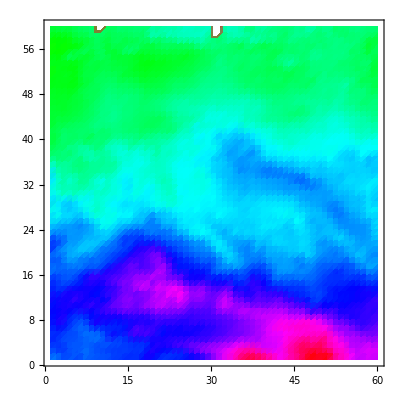

```mathematica
ListDensityPlot[FillData[OzoneData,Method->ColumnInterpolation], ColorFunction -> Hue]
```

There are three missing values located at the North Pole. We can use another method in a second pass to fill them.

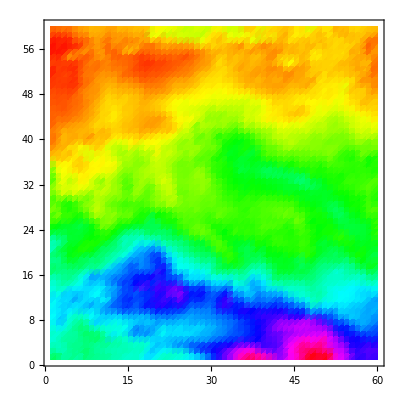

```mathematica
ListDensityPlot[FillData[FillData[OzoneData,Method->ColumnInterpolation],Method->SmoothFill],ColorFunction->Hue]
```

As we mentioned, ColumnInterpolation is preferred over RowInterpolation for this data, in part because of the shape of the big block of missing values. The word “big”, however, means compared to the size of the structures that we see in the nonmissing parts of the data. The StructureSize option to FillData can be used by both interpolation methods and allows us to specify the size of structures in the data; FillData will not interpolate across sections of rows or columns where the number of missing values is greater than or equal to this number.

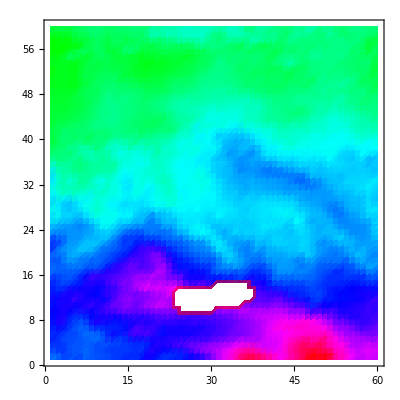

```mathematica
ListDensityPlot[FillData[OzoneData,Method->RowInterpolation,StructureSize->5], ColorFunction -> Hue]
```

So far we have assumed that data values of zero were the missing ones. The MissingIs option allows us to choose another value.

```mathematica
MatrixForm[FillData[myData1,MissingIs->15]]
```

(10. | 7. | 6. | 7. | 10. | 10.
9. | 6. | 0. | 6. | 9. | 0.
10. | 0. | 0. | 7. | 10. | 0.
13. | 10. | 9. | 10. | 0. | 0.
18. | 13. | 14. | 9. | 0. | 0.)

Here the 15 in the upper right corner has been replaced by the value of its neighbor, 10.

```mathematica
MatrixForm[N[FillData[myData1,MissingIs->15,Method->SmoothFill],3]]
```

(10. | 7. | 6. | 7. | 10. | 6.33333
9. | 6. | 0. | 6. | 9. | 0.
10. | 0. | 0. | 7. | 10. | 0.
13. | 10. | 9. | 10. | 0. | 0.
18. | 12.8 | 14. | 6.6 | 0. | 0.)

Now the missing value in the upper right corner has been replaced by the mean of 10, 9, and 0.

### 6.1.7 References

William S. Cleveland, Visualizing Data (AT&T Bell Labs, 1993). The principles of loess fitting are discussed with clarity throughout this book

Brand Fortner, The Data Handbook (SpyGlass Inc., 1992), Chapter 11. A survey of techniques for filling missing data, many of which are used by the EDA function FillData

K.S. Riedel and A. Sidorenko, Computers in Physics 8 (1994), 402. A tutorial on the sometimes sophisticated algorithms used to smooth noise in a data set

## 6.2 Details

### 6.2.1 Nonmonotonic Data and Related Assumptions

When the dependent variable is not monotonic, the results from the EDA functions discussed in this chapter may be incorrect.

The default behavior of SmoothData, which is just a simple average, weakly assumes that the data is monotonic. This method does not handle local minima or maxima in the data very well.

The WeightedAverage method for SmoothData uses the values of the independent variable to choose the weights to multiply with the dependent variable. Thus, there is no assumption of monotonicity. This method does not handle local minima or maxima in the data very well.

The SimpleMedian method of SmoothData makes no assumption about monotonicity. This method does not handle local minima or maxima in the data very well.

The WeightedFourier method of SmoothData strongly assumes that the dependent variable is monotonic.

```mathematica
Needs["EDA`"]
```

```mathematica
SmoothData[Table[{i+RandomInteger[],i^2},{i,100}],Method->WeightedFourier];
```

SmoothData::notmonotonic: Warning: the independent variable is not monotonic. Results may
	have no meaning.

The WeightedFourier method handles local minima or maxima better than any other method available for SmoothData.

For nonmonotonic data for which smoothing with WeightedFourier is desired, it may be reasonable to use the Mathematica built-in function Interpolation on the data, and then use Table to form a data set that is monotonic in the independent variable.

LoessFit makes no assumptions about the independent variable being monotonic, since it uses the independent variable to calculate the weights to multiply with the dependent variable. Particularly for polynomial fit or order greater than 1, it also handles local minima and maxima in the data very well.

### 6.2.2 Comparing Various Smoothing Methods

Most of the smoothing examples in this chapter have concentrated on the “chirp” signal. Here we discuss some of the issues in selecting one of the methods available in this package.

First we generate some noisy data for a parabola.

```mathematica
SeedRandom[12345];
N[try=Table[{i,i^2+RandomReal[{-2,2}]},{i,1,10,0.5}];]
```

```mathematica
Needs["EDA`"]
```

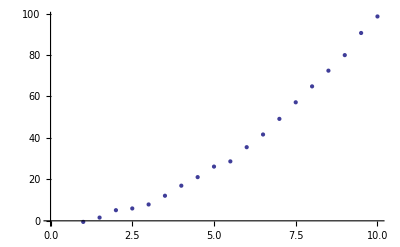

```mathematica
EDAListPlot[try]
```

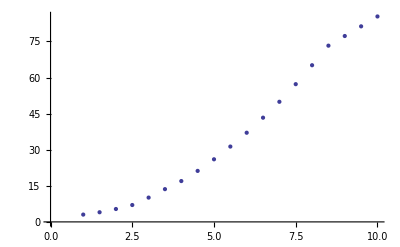

```mathematica
EDAListPlot[SmoothData[try]]
```

Clearly the right-hand side, where the data is beginning to increase rapidly, is pulled down from a reasonable value by this procedure. Now extract the y values from try and plot the residuals between them and the result of SmoothData.

```mathematica
y=Last/@try;
```

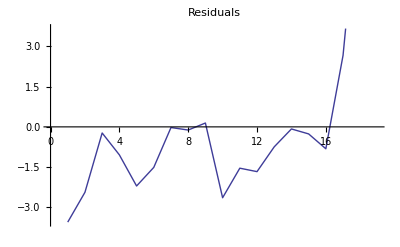

```mathematica
EDAListPlot[y-Last/@SmoothData[try],PlotLabel->"Residuals",Joined->True]
```

Reducing the number of points in each subset used by SmoothData helps somewhat.

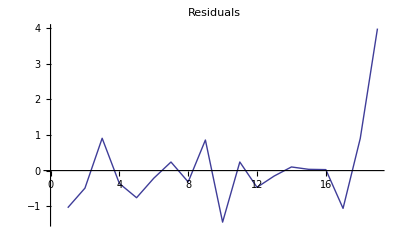

```mathematica
EDAListPlot[y-Last/@SmoothData[try,Points->3],PlotLabel->"Residuals",Joined->True]
```

A moment’s thought makes it clear that this method will always have these kinds of difficulties at any edge where the slope is significant.

We now examine the WeightedAverage method.

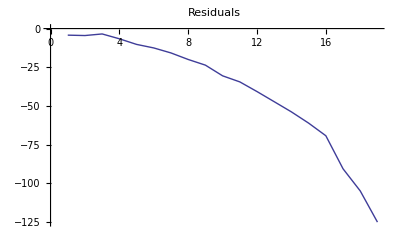

```mathematica
EDAListPlot[y-Last/@SmoothData[try,Method->WeightedAverage],PlotLabel->"Residuals",Joined->True]
```

The graph shows that the method gives values much too large at the right-hand side. We reduce the number of points.

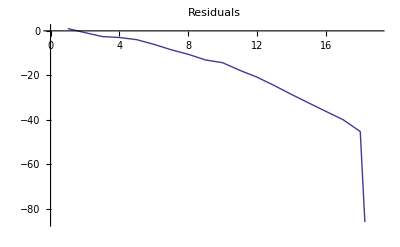

```mathematica
EDAListPlot[y-Last/@SmoothData[try,Method->WeightedAverage,Points->3],PlotLabel->"Residuals",Joined->True]
```

This change helps all but the very last result. Again, this behavior is a general feature of this method near an edge with a large slope.

We examine the SimpleMedian method.

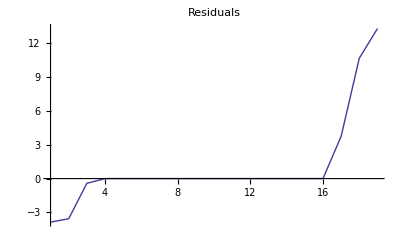

```mathematica
EDAListPlot[y-Last/@SmoothData[try,Method->SimpleMedian],PlotLabel->"Residuals",Joined->True, PlotRange -> All]
```

This method is also having problems at the right-hand side, and some difficulty on the left. Reducing the number of points helps for this case.

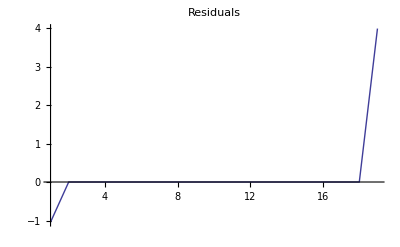

```mathematica
EDAListPlot[y-Last/@SmoothData[try,Method->SimpleMedian,Points->3],PlotLabel->"Residuals",Joined->True, PlotRange -> All]
```

For data with a larger noise component, reducing the number of points will usually worsen the result.

Next, we look at the WeightedFourier method.

SmoothData::bigsigma: Warning: the standard deviation of the weight function is very large.

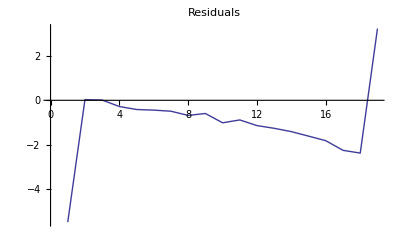

```mathematica
EDAListPlot[y-Last/@SmoothData[try,Method->WeightedFourier],PlotLabel->"Residuals",Joined->True]
```

This method is having problems on both the left and right sides. The warning message is due to the details of the Fourier transform; it is discussed in Section 6.2.2.1.

Finally, we will examine LoessFit for straight line and quadratic fits.

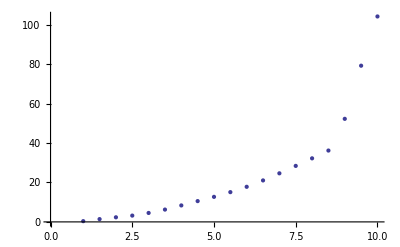

```mathematica
EDAListPlot[LoessFit[try,1]]
```

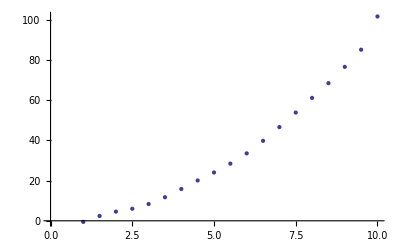

```mathematica
EDAListPlot[LoessFit[try,2]]
```

We extract and plot the residuals.

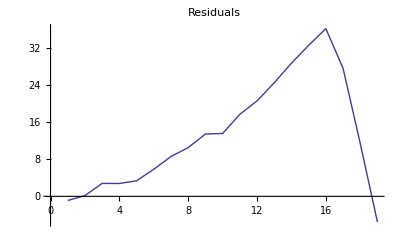

```mathematica
EDAListPlot[y-Last/@LoessFit[try,1],PlotLabel->"Residuals",Joined->True]
```

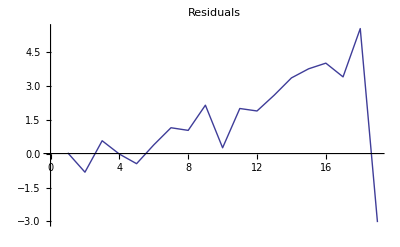

```mathematica
EDAListPlot[y-Last/@LoessFit[try,2],PlotLabel->"Residuals",Joined->True]
```

Notice that the values of the residuals are much smaller for the higher-order polynomial fit.

#### 6.2.2.1 More on the WeightedFourier Method

In the previous section, the WeightedFourier method of SmoothData generated a warning message.

EDAListPlot[y -
	(Last /@ SmoothData[try,
	Method -> WeightedFourier ]),
	PlotLabel -> "Residuals",
	Joined -> True  ];

SmoothData::bigsigma: Warning: the standard deviation of the weight function is very large.

Here we discuss what the message meant.

Because the data sets we are dealing with are collections of discrete points, the Fourier transform of the data will show “aliases” or “Nyquist pairs”. We will illustrate with a sampled sine wave.

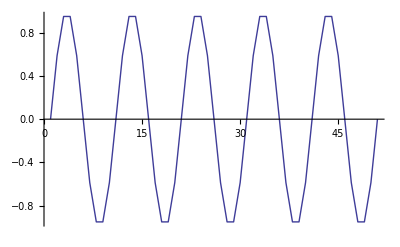

```mathematica
ListPlot[N[Table[Sin[t 2 π],{t,0,5,0.1}]],PlotRange->All,Joined->True]
```

We graph the Fourier transform.

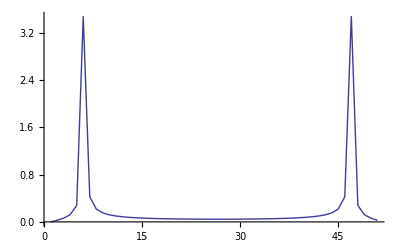

```mathematica
ListPlot[Abs[Fourier[N[Table[Sin[i 2 π],{i,0,5,0.1}]]]],PlotRange->All,Joined->True]
```

The WeightedFourier method of SmoothData weights the transform with a Gaussian, and due to these aliases, it actually weights both sides. So, for a standard deviation sigma of 5, the weighting can be graphed.

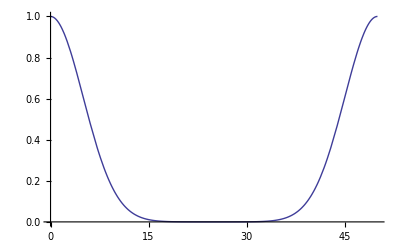

```mathematica
sigma=5;
Plot[ⅇ^(-x^2/(2 sigma^2))+ⅇ^(-(x-50)^2/(2 sigma^2)),{x,0,50}]
```

If Points is large, these two Gaussians can overlap.

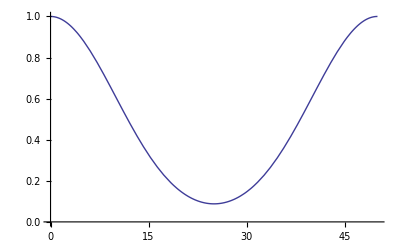

```mathematica
sigma=10;
Plot[ⅇ^(-x^2/(2 sigma^2))+ⅇ^(-(x-50)^2/(2 sigma^2)),{x,0,50},AxesOrigin->{0,0}]
```

This is the condition that generated the SmoothData::bigsigma message above. Since the standard deviation of the Gaussian scales as the square root of the number of points in each data subset, the message can often be suppressed by reducing the number of points using the Points option.

### 6.2.3 How LoessFit Works

This section discusses the details of LoessFit, and in particular why it works so well as a data smoother and a nonparametric fitter. We will do a LoessFit to the ganglion data we have looked at before.

```mathematica
Needs["EDA`"]
```

```mathematica
LoadData[Ganglion]
```

LoadData::name: Loading: GanglionData

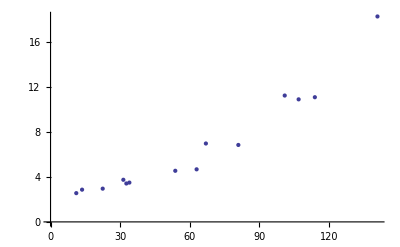

```mathematica
EDAListPlot[GanglionData]
```

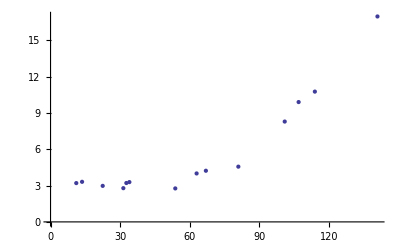

```mathematica
EDAListPlot[LoessFit[GanglionData,1,Points->13]]
```

First, LoessFit divides the data into a number of partitions. For example, here is the eighth data point.

```mathematica
GanglionData⟦8⟧
```

{63.,4.68}

We shall examine the eight partition of the data set. In order to do this, we follow the progress of LoessFit in Subsubsection 6.2.3.1 below and define there the variables to be used here.Null

```mathematica
x8 = {13.6,22.5,31.4,32.7,34.,53.8,63.,67.,81.,101.,107.,114.,141.};
```

```mathematica
y8 = {2.87,2.96,3.75,3.42,3.5,4.55,4.68,6.98,6.85,11.25,10.91,11.1,18.29};
```

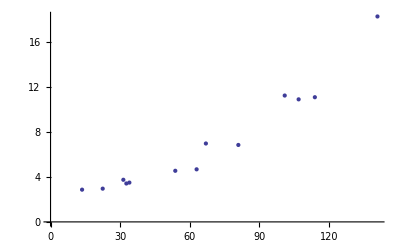

```mathematica
EDAListPlot[Transpose[{x8,y8}]]
```

The weights for each value of the independent variable, as found in Subsubsection 6.2.3.1, are displayed.

```mathematica
weights = {0.4150991039587969,0.6360894542733538,0.813490365139083,0.8342481002375427,0.8536069943711849,0.9950854008185341,1.,0.9995954624419067,0.9635827812877933,0.6916770971348261,0.5523690608005944,0.37398112945564055,2.2250738585072014*^-308};
```

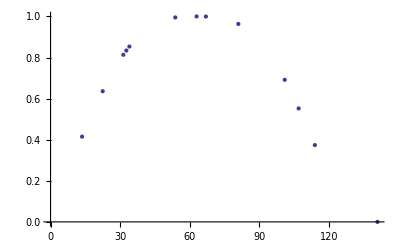

```mathematica
EDAListPlot[Transpose[{x8,weights}]]
```

Next we look at the weighted data for this partition.

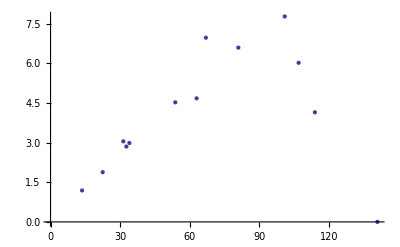

```mathematica
EDAListPlot[Transpose[{x8,weights y8}]]
```

We fit this to a straight line.

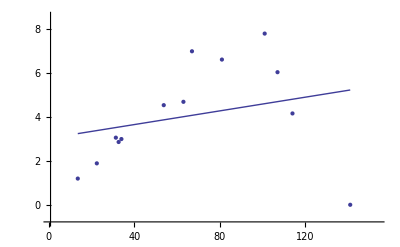

{a[0]→3.02232,a[1]→0.015568,PseudoErrorY→2.36871,SumOfSquares→61.7189,DegreesOfFreedom→11}

```mathematica
result=LinearFit[Transpose[{x8,weights y8}],{0,1},a,ReturnErrors->False]
```

Since we have chosen 13 points, the seventh member of this partition is the point we are trying to loess fit. Thus, the value that will replace the eighth value is calculated.

```mathematica
a[0]+a[1] x8⟦7⟧/.result
```

4.0031

#### 6.2.3.1 Digging Out Details From LoessFit

LoessFit accepts an option EDAShowProgress which provides many many details of its calculation. We will use that option to dig out the specifics we need in discussing how the program works.

```mathematica
Needs["EDA`"]
```

```mathematica
LoadData[Ganglion]
```

LoadData::name: Loading: GanglionData

```mathematica
LoessFit[GanglionData,2, Points -> 13,EDAShowProgress -> True]
```

14 datapoints, each with 2 variables.

Points = 13

Independent variable partitions: {{11.1,13.6,22.5,31.4,32.7,34.,53.8},{11.1,13.6,22.5,31.4,32.7,34.,53.8,63.},{11.1,13.6,22.5,31.4,32.7,34.,53.8,63.,67.},{11.1,13.6,22.5,31.4,32.7,34.,53.8,63.,67.,81.},{11.1,13.6,22.5,31.4,32.7,34.,53.8,63.,67.,81.,101.},{11.1,13.6,22.5,31.4,32.7,34.,53.8,63.,67.,81.,101.,107.},{11.1,13.6,22.5,31.4,32.7,34.,53.8,63.,67.,81.,101.,107.,114.},{13.6,22.5,31.4,32.7,34.,53.8,63.,67.,81.,101.,107.,114.,141.},{22.5,31.4,32.7,34.,53.8,63.,67.,81.,101.,107.,114.,141.},{31.4,32.7,34.,53.8,63.,67.,81.,101.,107.,114.,141.},{32.7,34.,53.8,63.,67.,81.,101.,107.,114.,141.},{34.,53.8,63.,67.,81.,101.,107.,114.,141.},{53.8,63.,67.,81.,101.,107.,114.,141.},{63.,67.,81.,101.,107.,114.,141.}}

Dependent variable partitions: {{2.56,2.87,2.96,3.75,3.42,3.5,4.55},{2.56,2.87,2.96,3.75,3.42,3.5,4.55,4.68},{2.56,2.87,2.96,3.75,3.42,3.5,4.55,4.68,6.98},{2.56,2.87,2.96,3.75,3.42,3.5,4.55,4.68,6.98,6.85},{2.56,2.87,2.96,3.75,3.42,3.5,4.55,4.68,6.98,6.85,11.25},{2.56,2.87,2.96,3.75,3.42,3.5,4.55,4.68,6.98,6.85,11.25,10.91},{2.56,2.87,2.96,3.75,3.42,3.5,4.55,4.68,6.98,6.85,11.25,10.91,11.1},{2.87,2.96,3.75,3.42,3.5,4.55,4.68,6.98,6.85,11.25,10.91,11.1,18.29},{2.96,3.75,3.42,3.5,4.55,4.68,6.98,6.85,11.25,10.91,11.1,18.29},{3.75,3.42,3.5,4.55,4.68,6.98,6.85,11.25,10.91,11.1,18.29},{3.42,3.5,4.55,4.68,6.98,6.85,11.25,10.91,11.1,18.29},{3.5,4.55,4.68,6.98,6.85,11.25,10.91,11.1,18.29},{4.55,4.68,6.98,6.85,11.25,10.91,11.1,18.29},{4.68,6.98,6.85,11.25,10.91,11.1,18.29}}

Weights: {{1.,0.999398,0.943991,0.711047,0.659769,0.604961,2.22507×10^-308},{0.999611,1.,0.982559,0.866117,0.836432,0.803262,0.0980446,2.22507×10^-308},{0.950405,0.976191,1.,0.976191,0.964306,0.949112,0.277195,0.0149142,2.22507×10^-308},{0.808111,0.867654,0.982768,1.,0.999946,0.999568,0.748345,0.40754,0.250348,2.22507×10^-308},{0.90808,0.935816,0.990041,0.999979,1.,0.999979,0.914131,0.760273,0.666129,0.270019,2.22507×10^-308},{0.910219,0.935948,0.988317,0.999864,0.999983,1.,0.941325,0.823463,0.747676,0.394017,0.0116761,2.22507×10^-308},{0.266025,0.346281,0.634827,0.853273,0.876307,0.897013,1.,0.98933,0.968706,0.748021,0.139001,0.0297469,3.69483×10^-47},{0.415099,0.636089,0.81349,0.834248,0.853607,0.995085,1.,0.999595,0.963583,0.691677,0.552369,0.373981,2.22507×10^-308},{0.479198,0.701787,0.730013,0.756844,0.983069,0.999526,1.,0.979823,0.736331,0.597081,0.41148,2.22507×10^-308},{0.0823551,0.109448,0.140072,0.745735,0.921167,0.962371,1.,0.892953,0.775214,0.579312,2.22507×10^-308},{2.22507×10^-308,0.000175814,0.300712,0.567207,0.673696,0.926549,1.,0.997968,0.979456,0.510329},{2.22507×10^-308,0.230291,0.47643,0.583193,0.87049,0.998335,1.,0.997357,0.72649},{3.69483×10^-47,0.060225,0.143971,0.582764,0.970092,0.995291,1.,0.753025},{2.22507×10^-308,0.00311799,0.161731,0.64752,0.771541,0.880659,1.}}

Weighted y-values: {{2.56,2.86827,2.79421,2.66643,2.25641,2.11736,1.01241×10^-307},{2.559,2.87,2.90838,3.24794,2.8606,2.81142,0.446103,1.04133×10^-307},{2.43304,2.80167,2.96,3.66072,3.29792,3.32189,1.26124,0.0697982,1.5531×10^-307},{2.06876,2.49017,2.90899,3.75,3.41982,3.49849,3.40497,1.90729,1.74743,1.52418×10^-307},{2.32468,2.68579,2.93052,3.74992,3.42,3.49993,4.15929,3.55808,4.64958,1.84963,2.50321×10^-307},{2.33016,2.68617,2.92542,3.74949,3.41994,3.5,4.28303,3.85381,5.21878,2.69902,0.131356,2.42756×10^-307},{0.681024,0.993826,1.87909,3.19977,2.99697,3.13954,4.55,4.63007,6.76156,5.12394,1.56376,0.324539,4.10126×10^-46},{1.19133,1.88282,3.05059,2.85313,2.98762,4.52764,4.68,6.97718,6.60054,7.78137,6.02635,4.15119,4.06966×10^-307},{1.41843,2.6317,2.49664,2.64896,4.47296,4.67778,6.98,6.71178,8.28372,6.51415,4.56743,4.06966×10^-307},{0.308832,0.374314,0.490251,3.3931,4.31106,6.71735,6.85,10.0457,8.45758,6.43036,4.06966×10^-307},{7.60975×10^-308,0.00061535,1.36824,2.65453,4.7024,6.34686,11.25,10.8878,10.872,9.33392},{7.78776×10^-308,1.04782,2.22969,4.07069,5.96286,11.2313,10.91,11.0707,13.2875},{1.68115×10^-46,0.281853,1.00492,3.99193,10.9135,10.8586,11.1,13.7728},{1.04133×10^-307,0.0217636,1.10785,7.2846,8.41751,9.77531,18.29}}

Fit results: {{2.67581,2.74956,2.7783,2.44199,2.36231,2.27484,-0.0201218,-1.70127,-2.55388,-6.11871,-12.7783,-15.1357,-18.0956,-31.628},{2.68789,2.80731,3.01453,2.88145,2.83353,2.77835,1.04048,-0.340114,-1.05379,-4.09296,-9.89531,-11.9711,-14.5883,-26.6553},{2.53531,2.73606,3.19829,3.26639,3.24335,3.21189,1.69345,0.324128,-0.40259,-3.57306,-9.79409,-12.0485,-14.9051,-28.2071},{2.13763,2.39114,3.09169,3.47692,3.5068,3.52995,3.05102,2.29745,1.86472,-0.151406,-4.38504,-5.96563,-7.99077,-17.6292},{2.16378,2.41828,3.17783,3.70865,3.76704,3.82055,4.03234,3.74554,3.54461,2.47751,-0.0287115,-1.00582,-2.27716,-8.50634},{2.08039,2.35387,3.18196,3.78287,3.85163,3.91555,4.28989,4.08124,3.9148,2.97092,0.647404,-0.273354,-1.47807,-7.44121},{0.142031,0.629536,2.1629,3.38062,3.53207,3.67678,5.04848,5.15424,5.09502,4.38566,2.0174,0.996102,-0.37673,-7.50102},{-0.389728,0.107089,1.72476,3.10667,3.28879,3.46587,5.5413,6.10858,6.27664,6.48983,5.78239,5.33799,4.6841,0.795757},{-2.05777,-1.43552,0.598327,2.34899,2.581,2.80697,5.50183,6.27707,6.51974,6.91864,6.27293,5.80036,5.08636,0.691345},{-7.57729,-6.5988,-3.37339,-0.550862,-0.172306,0.197655,4.76997,6.21597,6.71039,7.79998,7.62719,7.17863,6.42387,1.17808},{-6.39398,-5.74193,-3.52276,-1.46302,-1.1755,-0.89139,3.01544,4.56222,5.1816,7.0958,9.14603,9.6041,10.0469,10.8311},{-5.82947,-5.32674,-3.57469,-1.8814,-1.63898,-1.39782,2.12028,3.65597,4.30408,6.47898,9.33371,10.1323,11.0302,14.1529},{-16.0784,-15.1043,-11.7613,-8.61306,-8.1695,-7.73009,-1.551,0.992203,2.03305,5.36632,9.29242,10.2785,11.3171,14.195},{-3.6992,-3.71865,-3.64602,-3.35193,-3.29043,-3.22421,-1.63157,-0.518563,0.0391659,2.34351,6.58608,8.07694,9.94349,18.4264}}

New y-values: {2.67581,2.80731,3.19829,3.47692,3.76704,3.91555,5.04848,6.10858,6.51974,7.79998,9.14603,10.1323,11.3171,18.4264}

{{11.1,2.67581},{13.6,2.80731},{22.5,3.19829},{31.4,3.47692},{32.7,3.76704},{34.,3.91555},{53.8,5.04848},{63.,6.10858},{67.,6.51974},{81.,7.79998},{101.,9.14603},{107.,10.1323},{114.,11.3171},{141.,18.4264}}

Now we cut-and-paste to define the values of the eight partition of the data.

```mathematica
x8 = {13.6,22.5,31.4,32.7,34.,53.8,63.,67.,81.,101.,107.,114.,141.};
```

```mathematica
y8 = {2.87,2.96,3.75,3.42,3.5,4.55,4.68,6.98,6.85,11.25,10.91,11.1,18.29};
```

Next we extract the tri-cubic weights used on this partition.

```mathematica
weights = {0.4150991039587969,0.6360894542733538,0.813490365139083,0.8342481002375427,0.8536069943711849,0.9950854008185341,1.,0.9995954624419067,0.9635827812877933,0.6916770971348261,0.5523690608005944,0.37398112945564055,2.2250738585072014*^-308};
```

## 6.3 Summary of the SmoothData Package

```mathematica
Needs["EDA`"]
```

```mathematica
Information["FillData",LongForm->False]
```

FillData[data] fills in missing values in the matrix of values "data".
	The default method is EDANearestNeighbor, and the routine determines which
	values are to be filled by the definition of MissingIs, which by default
	is 0.

```mathematica
TableForm[Options[FillData]]
```

MaximumIterations→1
Method→EDANearestNeighbor
MissingIs→0
StructureSize→∞

```mathematica
Information["MaximumIterations",LongForm->False]
```

MaximumIterations is an option for various routines that use	iterative techniques. It specifies the maximum number
	of iterations to perform before quitting.

```mathematica
Information["Method",LongForm->False]
```

Method is an option for various algorithm-intensive functions that specifies what internal methods they should use.

```mathematica
Information["EDANearestNeighbor",LongForm->False]
```

EDANearestNeighbor is the default method for FillData. This method fills
	in missing values with duplicates of an adjacent non-missing neighbor.
	Other methods are ColumnInterpolation, RowInterpolation, SmoothFill, and
	SmoothFillAll.

```mathematica
Information["ColumnInterpolation",LongForm->False]
```

ColumnInterpolation is an optional method for FillData. This method
	fills in missing values with interpolations from non-missing values in
	the same column.

```mathematica
Information["RowInterpolation",LongForm->False]
```

RowInterpolation is an optional method for FillData. This method
	fills in missing values with interpolations from non-missing values in
	the same row.

```mathematica
Information["SmoothFill",LongForm->False]
```

SmoothFill is an optional method for FillData. This method fills in
	missing values with the average of the 8 adjacent neighboring positions.

```mathematica
Information["SmoothFillAll",LongForm->False]
```

SmoothFillAll is an optional method for FillData. This method replaces
	all values in data with the average of the non-missing values in the 3x3
	matrix surrounding the data point.

```mathematica
Information["MissingIs",LongForm->False]
```

MissingIs defines the contents of cells in a matrix of data that 
	FillData assumes are missing data.

```mathematica
Information["StructureSize",LongForm->False]
```

StructureSize is an option for FillData when the method is 
	RowInterpolation or ColumnInterpolation that specifies the size of
	structures in the data. If a block of missing values is greater than
	the value of StructureSize, that block is not interpolated.

```mathematica
Information["LoessFit",LongForm->False]
```

LoessFit[data, lambda] performs a loess fit on data.
	The parameter lambda specifies the degree of the polynomial used
	in the fits. Lambda must be 1, 2, or 3. Explicit errors in
	data are ignored. The data must contain at least 4 points for
	lambda = 1, and more points than 4 for larger lambda.

```mathematica
TableForm[Options[LoessFit]]
```

EDAAlpha→Automatic
Points→Automatic
EDAShowProgress→False

```mathematica
Information["EDAAlpha",LongForm->False]
```

EDAAlpha is an option for LoessFit that selects the number of points
	used in each subset of the data. Automatic (the default) uses
	2*Floor[Sqrt[Length[data]]] + 1 points. Otherwise, the points are
	equal to the value of EDAAlpha times the number of data points in the
	data, rounded to the nearest odd integer. EDAAlpha should be a positive
	number. Note that the Points option provides another way
	to choose the points. The EDAAlpha option is used to make LoessFit
	more notationally consistent with William S. Cleveland, "Visualizing
	Data" (AT&T Bell Laboratories, 1993).

```mathematica
Information["Points",LongForm->False]
```

Points is an option for SmoothData and LoessFit that specifies the
	number of points to be used in smoothing. If set to Automatic (the
	default), the number of points is 2*Floor[Sqrt[Length[data]]] + 1.
	Otherwise, the value is used for the number of points. For both programs,
	the number of points is the size of each subset, except for the
	WeightedFourier method of SmoothData, in which case it is the
	the standard deviation squared of the Gaussian weighting.
	The number of points should be an odd number. For SmoothData, its
	value should be less than the number of data points.

```mathematica
Information["EDAShowProgress",LongForm->False]
```

EDAShowProgress is an option for various routines. When set to True, the
	routine will print messages showing its progress in performing
	its tasks. If set to False, no such information is printed.

```mathematica
Information["SmoothData",LongForm->False]
```

SmoothData[data] smooths data. A Method option allows various
	methods to be used: EDASimple (the default), SimpleMedian,
	WeightedAverage, or WeightedFourier. If 'data' contains
	explicit errors they are ignored, and SmoothData returns
	either a set of y values or {x, y} pairs.

```mathematica
TableForm[Options[SmoothData]]
```

Method→EDASimple
Points→Automatic

```mathematica
Information["Method",LongForm->False]
```

Method is an option for various algorithm-intensive functions that specifies what internal methods they should use.

```mathematica
Information["EDASimple",LongForm->False]
```

EDASimple is the default method used by SmoothData, in which each
	data point has the value of the dependent variable replaced by
	an average of it and its nearest neighbors.

```mathematica
Information["WeightedAverage",LongForm->False]
```

WeightedAverage is a type of method for SmoothData. When this
	method is chosen, the data is weighted with a parabola whose
	maximum is 1.5 at the center of the set of points.

```mathematica
Information["SimpleMedian",LongForm->False]
```

SimpleMedian is a method for SmoothData. When this method
	is chosen, a local median of the data is used to smooth the data.

```mathematica
Information["WeightedFourier",LongForm->False]
```

WeightedFourier is a type of method for SmoothData. The Fourier
	transform of the data is weighted with a Gaussian centered at zero
	frequency, and the inverse Fourier transform of the result is taken.

```mathematica
Information["SmoothTestData",LongForm->False]
```

SmoothTestData[number, stddev] generates number data points which are
	of the form Sin[4Pi t^2] for t between 0 and 1, with a Gaussian noise
	of standard deviation stddev added. If the option ExtraSignal is set
	to True, a sine wave of period 0.05 and amplitude 0.5 is added to the
	chirp between t = 0.4 and t = 0.45.

```mathematica
Options[SmoothTestData]
```

{ExtraSignal→False}

```mathematica
Information["ExtraSignal",LongForm->False]
```

ExtraSignal is an option for SmoothTestData. If set to True, a sine 
	wave of period 0.05 and amplitude 0.5 is added to the chirp 
	between t = 0.4 and t = 0.45.